```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

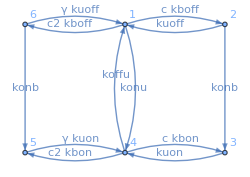

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
(*Laplace transform of FPTs for individual hitting states*)
Fon = LaplaceTransformFPT[Q2,s2];
F31 = Fon[[3,1]][[1]];
F41 = Fon[[4,1]][[1]];
F51 = Fon[[5,1]][[1]];
```

```mathematica
(*Laplace for hitting set, joint with the hitting state*)
ClearAll[Foff1on];
offStates = {6,1,2};
onStates = {5,4,3};
Foff1on = LaplaceTransformToSetByState[Q2,1,onStates,s1];
FoffOn = Foff1on[[3]][[1]]*F31 +Foff1on[[2]][[1]]*F41 + Foff1on[[1]][[1]]*F51; (*F1off[[2]][[1]]*F41 +*)
```

```mathematica
(*Means, variances and covariances of FPTs from the Laplace transforms*)
partials1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,1}]]];
partials2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,1}]]];
partials1s1 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s1,2}]]];
partials2s2 = With[{s1=0, s2=0}, Evaluate[D[FoffOn, {s2,2}]]];
partials1s2 = With[{s1=0, s2=0}, Evaluate[D[D[FoffOn, {s2,1}],{s1,1}]]];
```

```mathematica
meanToffLt = -partials1;
meanTonLt = -partials2;
varToffLt = partials1s1 - meanToffLt^2;
varTonLt = partials2s2 - meanTonLt^2;
covTonToff = partials1s2 - meanToffLt*meanTonLt;
τ = Simplify[meanToffLt + meanTonLt,assum];
```

```mathematica
τfun[c_?NumericQ,c2_?NumericQ,γ_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ ]:=Evaluate[τ];
```

```mathematica
ClearAll[FisherSafe]
ClearAll[FisherRate]

FisherRate[c0i_,c2i_,γi_,kboffi_,konbi_,kuoni_,kboni_,koffui_,kuoffi_,konui_ ]:=Module[{FoffOnPartEval,PjointPartEval,d2LogPjointPartEval,τPartialEval,Fjoint,Pjoint,integrand,integral},
FoffOnPartEval=FoffOnfun[c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui] ;
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];

PjointPartEval=InverseLaplaceTransform[FoffOnPartEval,{s1,s2},{t1,t2}];
d2LogPjointPartEval=D[Log[PjointPartEval],{c,2}];
integrand=Evaluate[PjointPartEval* d2LogPjointPartEval/.c->c0i];

integral=-NIntegrate[integrand,{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10];
c0i^2*integral/τPartialEval
];
```

```mathematica
ClearAll[expr1];
ClearAll[expr2];
ClearAll[exprS1];
ClearAll[exprS12];
expr1 = FoffOn /.{γ->2};
expr2=Factor[expr1,Modulus->0];
exprS1=Apart[expr2,s1];  (*treat s2,parameters as constants*)
exprS12=Apart[exprS1,s2]
```

(2 c kboff koffu konb^2 kuon^2+2 c2 kboff koffu konb^2 kuon^2+2 koffu konb^2 konu kuon^2+4 c kboff koffu konb kuoff kuon^2+2 c2 kboff koffu konb kuoff kuon^2+6 koffu konb konu kuoff kuon^2+4 koffu konu kuoff^2 kuon^2+2 c kboff koffu konb kuon^2 s1+2 c2 kboff koffu konb kuon^2 s1+4 koffu konb konu kuon^2 s1+6 koffu konu kuoff kuon^2 s1+2 koffu konu kuon^2 s1^2+c kboff koffu konb^2 kuon s2+2 c2 kboff koffu konb^2 kuon s2+3 koffu konb^2 konu kuon s2+2 c kboff koffu konb kuoff kuon s2+2 c2 kboff koffu konb kuoff kuon s2+9 koffu konb konu kuoff kuon s2+6 koffu konu kuoff^2 kuon s2+c kboff koffu konb kuon s1 s2+2 c2 kboff koffu konb kuon s1 s2+6 koffu konb konu kuon s1 s2+9 koffu konu kuoff kuon s1 s2+3 koffu konu kuon s1^2 s2+koffu konb^2 konu s2^2+3 koffu konb konu kuoff s2^2+2 koffu konu kuoff^2 s2^2+2 koffu konb konu s1 s2^2+3 koffu konu kuoff s1 s2^2+koffu konu s1^2 s2^2)/((c kboff konb^2+c2 kboff konb^2+konb^2 konu+2 c kboff konb kuoff+c2 kboff konb kuoff+3 konb konu kuoff+2 konu kuoff^2+2 c kboff konb s1+2 c2 kboff konb s1+konb^2 s1+2 konb konu s1+2 c kboff kuoff s1+c2 kboff kuoff s1+3 konb kuoff s1+3 konu kuoff s1+2 kuoff^2 s1+c kboff s1^2+c2 kboff s1^2+2 konb s1^2+konu s1^2+3 kuoff s1^2+s1^3) (2 koffu kuon^2+2 c kbon kuon s2+c2 kbon kuon s2+3 koffu kuon s2+2 kuon^2 s2+c kbon s2^2+c2 kbon s2^2+koffu s2^2+3 kuon s2^2+s2^3))

```mathematica
exprS12Simpl=Simplify[exprS12]
```

(koffu (c kboff konb kuon (konb+2 kuoff+s1) (2 kuon+s2)+(konb+kuoff+s1) (kuon+s2) (2 c2 kboff konb kuon+konu (konb+2 kuoff+s1) (2 kuon+s2))))/((c kboff (konb+s1) (konb+2 kuoff+s1)+(konb+kuoff+s1) (c2 kboff (konb+s1)+(konu+s1) (konb+2 kuoff+s1))) (c kbon s2 (2 kuon+s2)+s2 (kuon+s2) (c2 kbon+2 kuon+s2)+koffu (2 kuon^2+3 kuon s2+s2^2)))

```mathematica
ClearAll[Pjoint];
Pjoint=InverseLaplaceTransform[exprS12,{s1,s2},{t1,t2},Assumptions->assum];
```

```mathematica
PjointSimpl=Simplify[Pjoint,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konu (konb+kuoff)),B==c kbon+c2 kbon+koffu+kuon,D==-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2}]
```

1/(4 √A √D)ⅇ^(-1/2 (√A+c kboff+c2 kboff+konb+konu+kuoff) t1-1/2 (B+√D) t2) koffu (√A (1+ⅇ^(√A t1)) konu (B-B ⅇ^(√D t2)+√D (1+ⅇ^(√D t2))+2 (-1+ⅇ^(√D t2)) kuon)+(-1+ⅇ^(√A t1)) (-c2 √D kboff konu-c2 √D ⅇ^(√D t2) kboff konu-c √D (1+ⅇ^(√D t2)) kboff konu+√D konb konu+√D ⅇ^(√D t2) konb konu-√D konu^2-√D ⅇ^(√D t2) konu^2+B (-1+ⅇ^(√D t2)) konu (c kboff+c2 kboff-konb+konu-kuoff)+√D konu kuoff+√D ⅇ^(√D t2) konu kuoff-4 c2 kboff konb kuon+4 c2 ⅇ^(√D t2) kboff konb kuon+2 c (-1+ⅇ^(√D t2)) kboff (2 konb-konu) kuon+2 c2 kboff konu kuon-2 c2 ⅇ^(√D t2) kboff konu kuon-2 konb konu kuon+2 ⅇ^(√D t2) konb konu kuon+2 konu^2 kuon-2 ⅇ^(√D t2) konu^2 kuon-2 konu kuoff kuon+2 ⅇ^(√D t2) konu kuoff kuon))

```mathematica
integrand =D[Pjoint,{c,1}]^2/Pjoint;(*-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2*)
```

```mathematica
integrandSimpl1=integrand//.{c kbon+c2 kbon+koffu+kuon->Bon,
-4 koffu kuon+(c kbon+c2 kbon+koffu+kuon)^2->D,
(-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2)->-Boff/2,
-(c kbon)/2-(c2 kbon)/2-koffu/2-kuon/2->-Bon/2,(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff)->A,(-4 kboff konb+2 kboff (c kboff+c2 kboff+konb+konu+kuoff))->E}
```

```mathematica
integrandC=Compile[{{c,_Real},{c2,_Real},{t1,_Real},{t2,_Real},{kboff,_Real},{konb,_Real},{kuon,_Real},{kbon,_Real},{koffu,_Real},{kuoff,_Real},{konu,_Real}},
Evaluate[integrand],
CompilationTarget->"C",
RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
integrandC[1,1,1,1,1,1,1,1,1,1,1.]
```

0.00346896

```mathematica
ClearAll[integrandCNum];
integrandCNum[c_?NumericQ,c2_?NumericQ,t1_?NumericQ,t2_?NumericQ,kboff_?NumericQ,konb_?NumericQ,kuon_?NumericQ,kbon_?NumericQ,koffu_?NumericQ,kuoff_?NumericQ,konu_?NumericQ]:=integrandC[N[c],N[c2],N[t1],N[t2],N[kboff],N[konb],N[kuon],N[kbon],N[koffu],N[kuoff],N[konu]];
```

```mathematica
integrandCNum[1,3,1,1,1,1,1,1,1,1,1]
```

0.00107171

```mathematica
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=0.;
c2=ω*c0;
γ=1;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
integral=-NIntegrate[integrandCNum[c0,c2,t1,t2,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->1}, 
PrecisionGoal->4,
AccuracyGoal->4,
MinRecursion->3,
MaxRecursion->10];
integral*c0^2/τfun[c0,c2,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
(*τfun[c_,c2_,γ_,kboff_,konb_,kuon_,kbon_,koffu_,kuoff_,konu_ ]*)
```

0.806061

```mathematica
ClearAll[FisherFast];
ClearAll[FisherSafe];
FisherFast[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=Module[{τPartialEval,integral},
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
integral=-NIntegrate[integrandCNum[c0i,c2i,t1,t2,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui],{t1,0,∞},{t2,0,∞},
Method->{"DoubleExponential","SymbolicProcessing"->0}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->6];
integral*c0i^2/τPartialEval];
```

```mathematica
FisherNum[c0i_?NumericQ,c2i_?NumericQ,γi_?NumericQ,kboffi_?NumericQ,konbi_?NumericQ,kuoni_?NumericQ,kboni_?NumericQ,koffui_?NumericQ,kuoffi_?NumericQ,konui_?NumericQ ]:=NIntegrate[Module[{f0,fp,fm,dlog,PjointPartEval,τPartialEval},
τPartialEval=τfun[c0i,c2i,γi,kboffi,konbi,kuoni,kboni,koffui,kuoffi,konui];
PjointPartEval=Pjoint/.{konb->konbi,kuon->kuoni, koffu->koffui,kboff->kboffi,kbon->kboni,konu->konui,kuoff->kuoffi};
f0=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i};
fp=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i+δ};
fm=PjointPartEval/. {t1->t1i,t2->t2i,c->c0i-δ};
(*central-difference derivative of log-pdf*)
dlog=(Log[fp]-Log[fm])/(2 δ);
N[dlog^2*f0*c0i^2/τPartialEval,20]],{t1i,0,∞},{t2i,0,∞},
Method->{"GlobalAdaptive","SymbolicProcessing"->1}, 
PrecisionGoal->6,
AccuracyGoal->6,
MinRecursion->3,
MaxRecursion->10,
WorkingPrecision->20];

ClearAll[FisherSafe];
FisherSafe[pars__?NumericQ]:=
Quiet[
Check[
FisherFast[pars],
-1,(* ← penalty when NIntegrate fails*)
{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
],{NIntegrate::ncvb,NIntegrate::inumri,NIntegrate::slowcon}
];
```

```mathematica
kmin =0.001;
kmax = 5.;
kdl=0.0888;
c0=40.;
ω=0.;
c2=ω*c0;
γ=1.;
kbofflim =Evaluate[Min[kdl,5*0.503427/c0]];
FisherSafe[c0,c2,γ,kbofflim,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.806061

```mathematica
FisherSafeLog[c0_,c2_,γ_,lnkboff,lnkonb,lnkuon,lnkbon,lnkoffu,lnkuoff,lnkonu]:=FisherSafe[c0,c2,γ,Exp[lnkboff],Exp[lnkonb],Exp[lnkuon],Exp[lnkbon],Exp[lnkoffu],Exp[lnkuoff],Exp[lnkonu]];
```

```mathematica
ClearAll[TestFun];
TestFun[c0_,kboff_,kbon_,kuoff_,konu_ ]:=Module[{},
Pause[1];
-(kboff-kdl)^2-(kbon-kdl)^2-(kuoff-3)^2-(konu-4)^2+c0];
```

```mathematica
cvals=10^Range[-1.,2.,3/27];
```

```mathematica
ω=0.1;
γ=1.;
kmin =0.0001;
kmax = 5;
kdl=0.0888;

(*Save the data*)
dir = ".julia/dev/LLROpt/mathematica-nbs";
datadir = FileNameJoin[dir,"data"];
plotdir = FileNameJoin[dir,"plots"];
date = "20250504";
```

```mathematica
(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
evals=0;
ParallelDo[
results=Reap[
Catch[
TimeConstrained[
NMaximize[
{TestFun[cvals[[i]],kboff,kbon,kuoff,konu],
kmin<=kboff<=kdl,
kmin<=kbon<=kdl,
kmin<=kuoff<=kmax,
kmin<=konu<=kmax},
{kboff,kbon,kuoff,konu},
Method->"NelderMead",
PrecisionGoal->6,AccuracyGoal->6,MaxIterations->10
],2,Throw["timeout",$tag]
],$tag
]
];
Save[FileNameJoin[{$HomeDirectory},datadir, date, "test-output-pid"<>ToString[i]<>".wl"],results]
,{i,1,28}
]
```

```mathematica
ClearAll[f,timedRun]

(*a toy integrand that Sows something each time it is called*)
f[x_]:=(Sow[{x}];Pause[1];1/(1+x^2));

(*-----------------------------------------------------------*)
(*timedRun[...] runs expr for at most t seconds.*)
(*It returns {result,listOfSows} if finished,*)
(*or {"timeout",listOfSows} if it hit the limit.*)
(*-----------------------------------------------------------*)
timedRun[expr_,t_]:=Reap@Catch[
TimeConstrained[expr,(*the job*)
t,
Throw["timeout",$tag]                          (*on timeout*)
],$tag                                              (*Catch label*)
];
```

```mathematica
timedRun[NIntegrate[Evaluate@f[x],{x,0,∞}],(*integrand Sows each call*)
0.0001                                   (*time limit in seconds*)
]
```

{1.5708,{}}

```mathematica
f[i_]:=results[[i]];
```

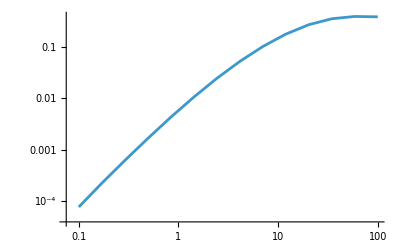

```mathematica
ListLinePlot[Table[{cvals[[i]],results[[i]]},{i,1,14}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
i=14;(*c0,c2,γ,kboff,konb,kuon,kbon,koffu,kuoff,konu*)
kdl=5*0.503427/100;
FisherSafe[cvals[[i]],0*cvals[[i]],γ,kdl,kmax,kmax,kmin,kmax,kmin,kmin]
```

0.804384

```mathematica
(*Joint PDF of OFF durations*)
ClearAll[Poff];
ClearAll[d2LogPoff];
ClearAll[integrandOff];

Foff=Foff1on[[3]][[1]] +Foff1on[[2]][[1]] + Foff1on[[1]][[1]];
expr1off = Foff /.{γ->5};
expr2off=Factor[expr1off,Modulus->0];
exprS1off=Apart[expr2off,s1]
```

(c kboff konb^2+c2 kboff konb^2+konb^2 konu+5 c kboff konb kuoff+c2 kboff konb kuoff+6 konb konu kuoff+5 konu kuoff^2+c kboff konb s1+c2 kboff konb s1+2 konb konu s1+6 konu kuoff s1+konu s1^2)/(c kboff konb^2+c2 kboff konb^2+konb^2 konu+5 c kboff konb kuoff+c2 kboff konb kuoff+6 konb konu kuoff+5 konu kuoff^2+2 c kboff konb s1+2 c2 kboff konb s1+konb^2 s1+2 konb konu s1+5 c kboff kuoff s1+c2 kboff kuoff s1+6 konb kuoff s1+6 konu kuoff s1+5 kuoff^2 s1+c kboff s1^2+c2 kboff s1^2+2 konb s1^2+konu s1^2+6 kuoff s1^2+s1^3)

```mathematica
Poff=InverseLaplaceTransform[exprS1off,{s1},{t1},Assumptions->assum]
```

```mathematica
(*A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff)-B/2==-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2*)
Simplify[Poff,{A==(c kboff+c2 kboff+konb+konu+kuoff)^2-4 (c kboff konb+c2 kboff konb+konb konu+konu kuoff),-B/2==-(c kboff)/2-(c2 kboff)/2-konb/2-konu/2-kuoff/2}]
```

$Aborted

Poff

```mathematica
d2LogPoff =D[Log[Poff],{c,2}];
integrandOff = Poff *d2LogPoff;
```

```mathematica
integrandOff/.{t1->0.1,c->1., c2->1., kboff->2., kbon->2.,konb->3.,konu->1.,kuon->1.,kuoff->2.,kuon->1.}
```

-0.0695138

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*New definition of specificity*)

(*Edge lists and weights*)
edges={{1,2},{2,1},{1,6},{6,1},{7,3},{3,7},
	    {4,5},{5,4},{6,5},{7,1},{2,3},{4,1},{7,5},{4,3}};
weights={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,koffu,c2*kbon,c*kbon};
nstates = 7;
nedges = Length[edges];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges[[i,1]]->edges[[i,2]],{i,1,nedges}];
g=Graph[edges,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights)[[i]],0.55],{i,1,nedges}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,7,1},{3,2}}}];
```

```mathematica
coords=GraphEmbedding[g];
coords[[4]][[1]]=coords[[4]][[1]] - 0.1;
coords[[7]][[1]]=coords[[7]][[1]] + 0.1;
coords[[7]][[2]]=coords[[7]][[2]] - 0.1;
coords[[4]][[2]]=coords[[4]][[2]] + 0.1;
coords[[1]][[2]]=coords[[1]][[2]] - 0.1;
```

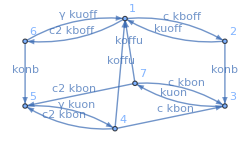

```mathematica
Graph[edges,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights)[[i]],0.55],{i,1,nedges}],ImageSize->250,VertexCoordinates->coords]
```